```mathematica
"3.1.1"
```

```mathematica
Plot[Log[x],{x,-4,4}]
```

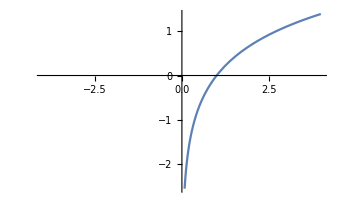
```mathematica
-Graphics-
"Risk averse; does not have values for negative numbers, this violates completude, transitivity, continuity and independece"
"3.1.2"
```

```mathematica
Plot[-ⅇ^-x,{x,-4,4}]
```

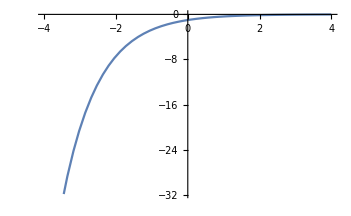
```mathematica
-Graphics-
"Risk Averse, The non-linearity violates only the independence axiom"
"3.1.3"
```

```mathematica
Plot[x^3,{x,-4,4}]
```

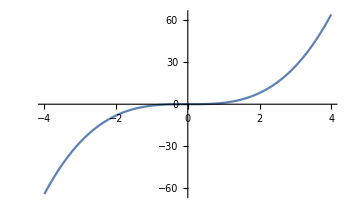
```mathematica
-Graphics-
"Utility monster, risk seeking but risk averse with negative values.The non-linearity violates only the independence axiom"
"3.1.4"
```

```mathematica
Plot[2x+2,{x,-4,4}]
```

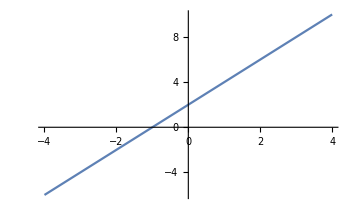
```mathematica
-Graphics-
"Risk Neutral, Does not violate any axioms"
"3.1.5"
```

```mathematica
Plot[x^7/7,{x,-6,6}]
```

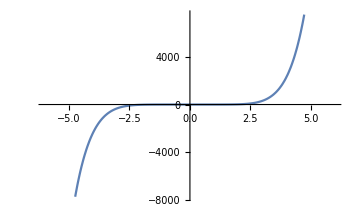
```mathematica
-Graphics-
"Utility monster, risk seeking but risk averse with negative values. When r is an odd integer greater than 1 then only the independence axiom is violated"
```

```mathematica
Plot[x^6/6,{x,-6,6}]
```

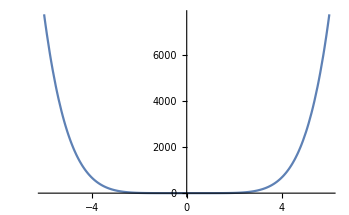
```mathematica
-Graphics-
"Risk seeking in every dimension. When r is an even integer greater than 1 then monotonicity and the independence axiom are violated"
```

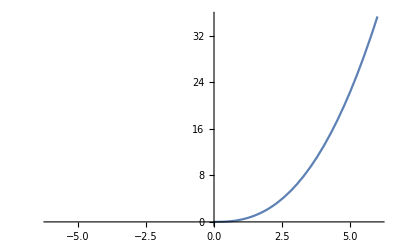

```mathematica
Plot[x^2.5/2.5,{x,-6,6}]
```

```mathematica
"Risk seeking; When r is greater than 1 but not an integer and then the function is convex, violates continuity/transitivity/independece"
Plot[x^0.5/0.5,{x,-6,6}]
```

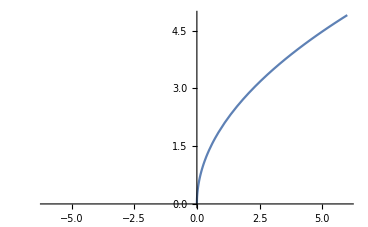
```mathematica
-Graphics-
"Risk Averse; When r is smaller than 1 the function is concave, it violates continuity/transitivity/transitivity "

"3.2.1, already answered"
"3.2.2"
w=169
p*√(w-25+g)+(1-p)*√(w-25)=√169
p*√(144+g)+(1-p)*√144=√169
p^2*(144+g)+(1-p)^2*144=169
g = 25/p^2+288/p-288=25/p^2+288(1/p-1);
"3.2.3"
p*√(w-60+1380)+(1-p)*√(w-60)=√w
p*√(w+1320)+(1-p)*√(w-60)=√w
p^2*(w+1320)+(1-p)^2*(w-60)=w
p^2*(w+1320)+(1-2p+p^2)(w-60)=w
wp^2+1320 p^2+w-w2p+wp^2-60+120p-60 p^2=w
2 wp^2+1320 p^2-2wp-60+120p-60 p^2=0
w(2 p^2-2p)=60 p^2-120p+60-1320 p^2
w2p(p-1)=60p(p-2-22p)+60
w2p(p-1)=60(p(p-2-22p)+1).b2
wp(p-1)=30(p(p-2-22p)+1)
w=(30(p(p-2-22p)+1))/(p(p-1))
"3.3.1"
E(w)=1/2(10+30)√λ-λ
(δE(w))/δλ=1/4(10+30)λ^(-1/2)-1=0
4=40 λ^(-1/2)
1/10=λ^(-1/2)
100 = λ
w=100;
"3.3.2"
k=1/1000;
u(w)=E(w)-kσ^2(w);
u(w)=E(w(λ))-1/1000 σ^2(w(λ));
σ^2(w(λ))=(30 √λ-λ-E(w))^2 1/2+(10 √λ-λ-E(w))^2 1/2
σ^2(w(λ))=(30 √λ-λ-20 √λ+λ)^2 1/2+(10 √λ-λ-20 √λ+λ)^2 1/2
σ^2(w(λ))=(10 √λ)^2 1/2+(-10 √λ)^2 1/2
σ^2(w(λ))=100λ 1/2+100λ 1/2=100λ
u(w)=1/2(40)√λ-λ-1/10 λ
(δu(w))/δλ=1/4(40)λ^(-1/2)-1-1/10=0
(δu(w))/δλ=1/4(40)λ^(-1/2)=1.1
(δu(w))/δλ=(40)λ^(-1/2)=4.4
(δu(w))/δλ=λ^(-1/2)=1.1/10
(δu(w))/δλ=λ=(100/11)^2=10000/121=82.6444
"3.3.3"
u(λ)=√(20 √λ-λ)
f[x_]:=√(20 √x-x)
```

```mathematica
f[x_]:=√(20 √x-x)
f'[x]
```

```mathematica
(-1+10/(√x))/(2 √(20 √x-x))
λ=x=10
```

```mathematica
"3.4.1"
u(w)=2w; if w⩽100
u(w)=w+100;if w>100

E(u(w))=.25*180+.75*210=45+157.5=202.5;
w=102.5
p=2.5
π=E(x)-p=2.5
```

```mathematica
"3.6.1"
Clear[x]
f[x_]:=-ⅇ^(-2*x)
f'[x]
f''[x]
-f''[x]/f'[x]
```

```mathematica
Clear[x]
Clear[w]
Integrate[-ⅇ^(-2(x+w)),{x,-0.4,0.6}]
```

-0.962173 ⅇ^(-2. w)

```mathematica
Clear[x]
Clear[w]
Integrate[-ⅇ^(-2(x+w)),x]
Simplify[1/2(ⅇ^(-2(-0.4+w))-ⅇ^(-2(0.6+w)))]
Log[-Simplify[1/2(ⅇ^(-2(0.6+w))-ⅇ^(-2(-0.4+w)))]]
```

1/2 ⅇ^(-2 w-2 x)

0.962173 ⅇ^(-2 w)

Log[0.962173 ⅇ^(-2 w)]

```mathematica
Log[-Simplify[1/2(ⅇ^(-2(1+w))-ⅇ^(-2(w)))]]
```

Log[1/2 ⅇ^(-2 (1+w)) (-1+ⅇ^2)]

```mathematica
D[Log[1/2 ⅇ^(-2 (1+w)) (-1+ⅇ^2)], w]
```

-2

```mathematica
ⅇ^0.8
```

2.22554